# Phy 362 K Homework 6

Problem 1

### (a)

```mathematica
Simplify[Integrate[A^2*z^2*Exp[-2*α*z^2],{z,0,Infinity}],α∈Reals&&α>0]
```

(A^2 √(π/2))/(8 α^(3/2))

```mathematica
Simplify[Solve[(A^2 √(π/2))/(8 α^(3/2))==1,A],A∈Reals&&A>0]
```

{{A→-(2 2^(3/4) α^(3/4))/π^(1/4)},{A→(2 2^(3/4) α^(3/4))/π^(1/4)}}

```mathematica
(2 2^(3/4) α^(3/4))/π^(1/4)
```

(2 2^(3/4) α^(3/4))/π^(1/4)

```mathematica
A:=(2 2^(3/4) α^(3/4))/π^(1/4)
```

```mathematica
ψ[z_]:=A*z*Exp[-α*z^2]
```

```mathematica
Simplify[-(ℏ^2/(2*m))*Integrate[ψ[z]*D[ψ[z],{z,2}],{z,0,Infinity}],α∈Reals&&α>0]
```

(3 α ℏ^2)/(2 m)

```mathematica
T[α_]:=(3 α ℏ^2)/(2 m)
```

```mathematica
Simplify[m*g*Integrate[z*ψ[z]*ψ[z],{z,0,Infinity}],α∈Reals&&α>0]
```

(g m √(2/π))/(√α)

```mathematica
V[α_]:=(g m √(2/π))/(√α)
```

```mathematica
H[α_]:=T[α]+V[α]
```

```mathematica
D[H[α],{α,1}]
```

-(g m)/(√(2 π) α^(3/2))+(3 ℏ^2)/(2 m)

```mathematica
Simplify[Solve[-(g m)/(√(2 π) α^(3/2))+(3 ℏ^2)/(2 m)==0,α],α>0&&α∈Reals]
```

{{α→(2/π)^(1/3)/(3^(2/3) (ℏ^2/(g m^2))^(2/3))}}

```mathematica
H[(2/π)^(1/3)/(3^(2/3) (ℏ^2/(g m^2))^(2/3))]
```

((3/π)^(1/3) ℏ^2)/(2^(2/3) m (ℏ^2/(g m^2))^(2/3))+g m (6/π)^(1/3) (ℏ^2/(g m^2))^(1/3)

```mathematica
Simplify[((3/π)^(1/3) ℏ^2)/(2^(2/3) m (ℏ^2/(g m^2))^(2/3))+g m (6/π)^(1/3) (ℏ^2/(g m^2))^(1/3)]
```

(3 g m (3/π)^(1/3) (ℏ^2/(g m^2))^(1/3))/2^(2/3)

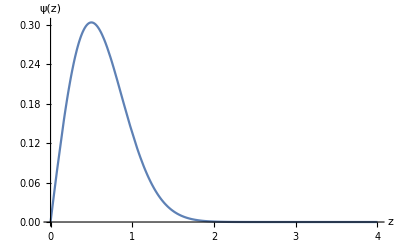

```mathematica
Plot[z*Exp[-2*z^2],{z,0,4},AxesLabel->{"z","ψ(z)"}]
```

### (b)

```mathematica
Solve[Integrate[Sqrt[2*m*(En-m*g*z)],{z,0,En/(m*g)}]==(n+3/4)*ℏ*π,En]
```

{{En→(g^(2/3) m^(1/3) (3+4 n)^(2/3) (-3 π)^(2/3) ℏ^(2/3))/(4 2^(1/3))},{En→-1/4 (-1/2)^(1/3) g^(2/3) m^(1/3) (3+4 n)^(2/3) (3 π)^(2/3) ℏ^(2/3)},{En→(g^(2/3) m^(1/3) (3+4 n)^(2/3) (3 π)^(2/3) ℏ^(2/3))/(4 2^(1/3))}}

```mathematica
Solve[(2 √2 En^2)/(3 g √(En m))==(n+3/4)*ℏ*π,En]
```

{{En→(g^(2/3) m^(1/3) (3+4 n)^(2/3) (-3 π)^(2/3) ℏ^(2/3))/(4 2^(1/3))},{En→-1/4 (-1/2)^(1/3) g^(2/3) m^(1/3) (3+4 n)^(2/3) (3 π)^(2/3) ℏ^(2/3)},{En→(g^(2/3) m^(1/3) (3+4 n)^(2/3) (3 π)^(2/3) ℏ^(2/3))/(4 2^(1/3))}}

### (d)

ParametricFunction[<>]

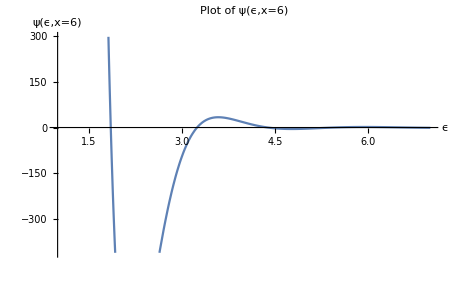

```mathematica
Clear[ϵ,ψ]
pfun=ParametricNDSolveValue[{-(1/2)*ψ''[x]+x*ψ[x]==ϵ*ψ[x],ψ[0]==0,ψ'[0]==3},ψ,{x,0,20},ϵ]
Plot[pfun[ϵ][6],{ϵ,1,7},PlotLabel->"Plot of ψ(ϵ,x=6)",AxesLabel->{"ϵ","ψ(ϵ,x=6)"}]
```

```mathematica
eps={FindRoot[pfun[ϵ][6],{ϵ,2}],FindRoot[pfun[ϵ][6],{ϵ,3}],FindRoot[pfun[ϵ][6],{ϵ,4.5}],FindRoot[pfun[ϵ][6],{ϵ,15.7}] }
```

{{ϵ→1.85576},{ϵ→3.24464},{ϵ→4.38491},{ϵ→14.1699}}

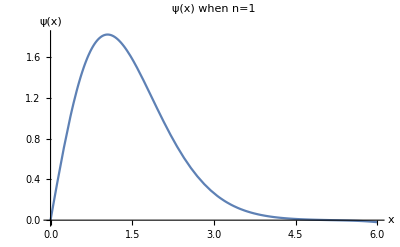

```mathematica
Plot[pfun[1.85576][x],{x,0,6},PlotLabel->"ψ(x) when n=1",AxesLabel->{"x","ψ(x)"}]
```

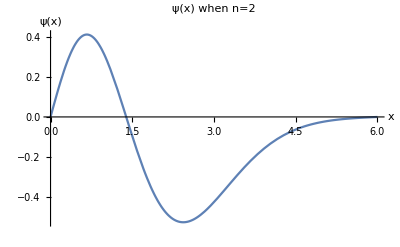

```mathematica
Plot[pfun[3.24464][x],{x,0,6},PlotLabel->"ψ(x) when n=2",AxesLabel->{"x","ψ(x)"}]
```

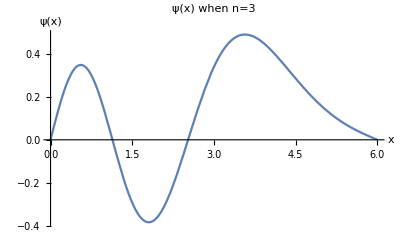

```mathematica
Plot[pfun[4.38491][x],{x,0,6},PlotLabel->"ψ(x) when n=3",AxesLabel->{"x","ψ(x)"}]
```

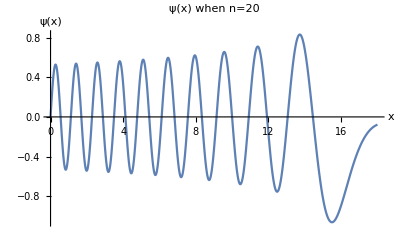

```mathematica
Plot[pfun[16.29999][x],{x,0,18},PlotLabel->"ψ(x) when n=20",AxesLabel->{"x","ψ(x)"}]
```

### (e)

```mathematica
Abs[0.48407*(9*Pi^2)^(1/3)-1.85576]/1.85576
Abs[0.65429*(9*Pi^2)^(1/3)-3.24464]/3.24464
Abs[0.80457*(9*Pi^2)^(1/3)-4.38491]/4.38491
Abs[(1/3)*(20+3/4)^(2/3)*(9*Pi^2)^(1/3)-16.29999]/16.29999
```

0.163859

0.100258

0.181314

0.311003

```mathematica
ℏ:=1.054571726*10^(-34)
```

```mathematica
Abs[(81/(4*Pi))^(1/3)-1.85576]/1.85576
```

0.00285138

Problem 2

### (b)

```mathematica
Clear[ψ,A,b]
ψ[x_]:=A*x*Exp[-b*x^2]
Simplify[Integrate[Abs[ψ[x]]^2,{x,-Infinity,Infinity}],A∈Reals&&b∈Reals&&A>0&&b>0]
```

(A^2 √(π/2))/(4 b^(3/2))

```mathematica
Solve[(A^2 √(π/2))/(4 b^(3/2))==1,A]
```

{{A→-2 b^(3/4) (2/π)^(1/4)},{A→2 b^(3/4) (2/π)^(1/4)}}

```mathematica
A:=2 b^(3/4) (2/π)^(1/4)
```

```mathematica
T[x_]:=-(ℏ^2/(2*m))*Integrate[ψ[x]*D[ψ[x],{x,2}],{x,-Infinity,Infinity}]
V[x_]:=(1/2)*m*ω^2*Integrate[x^2*ψ[x]*ψ[x],{x,-Infinity,Infinity}]
En[x_]:=T[x]+V[x]
```

```mathematica
En[x]
```

ConditionalExpression[(3 m ω^2)/(8 b)+(3 b ℏ^2)/(2 m),Re[b]>0]

```mathematica
T[x]
```

ConditionalExpression[(3 b ℏ^2)/(2 m),Re[b]>0]

```mathematica
D[En[x],{b,1}]
```

ConditionalExpression[-(3 m ω^2)/(8 b^2)+(3 ℏ^2)/(2 m),Re[b]>0]

```mathematica
Solve[-(3 m ω^2)/(8 b^2)+(3 ℏ^2)/(2 m)==0,b]
```

{{b→-(m ω)/(2 ℏ)},{b→(m ω)/(2 ℏ)}}

```mathematica
b:=(m ω)/(2 ℏ)
```

```mathematica
En[x]
```

ConditionalExpression[(3 ω ℏ)/2,Re[(m ω)/ℏ]>0]

Problem 3

### (a)

```mathematica
γ:=1/ℏ*Integrate[Sqrt[2m*(W-e*Ε*x)],{x,0,W/(e*Ε)}]
```

```mathematica
γ
```

(2 √2 W √(m W))/(3 e Ε ℏ)

### (b)

```mathematica
<<PhysicalConstants`
```

General::obspkg: "PhysicalConstants`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
W=Quantity[4.55,"eV"]
```

4.55

```mathematica
UnitConvert[W,"J"]
```

7.2899×10^-19

```mathematica
E0=(4/3)*(Sqrt[2*ElectronMass]/PlanckConstantReduced)*(UnitConvert[W,"Joule"]^(3/2)/ElectronCharge)
```

(√Kilogram (6.62971×10^10))/(Coulomb Joule Second)

```mathematica
E0
```

(√Kilogram (6.62971×10^10))/(Coulomb Joule Second)

```mathematica
UnitConvert[E0,"Volts/meter"]
```

UnitConvert[(√Kilogram (6.62971×10^10))/(Coulomb Joule Second),Volts/meter]

```mathematica
(6.62971*10^(10))/50
```

1.32594×10^9